```mathematica
(*Mathematica*)
```

```mathematica
A[n_]:=Table[If[m==k,0,If[m<k,(-1)^(m+k),-(-1)^(m+k)]],{k,1,n},{m,1,n}]
```

```mathematica
m=A[4]
```

{{0,1,-1,1},{-1,0,1,-1},{1,-1,0,1},{-1,1,-1,0}}

```mathematica
m.Transpose[m]
```

{{3,-2,0,2},{-2,3,-2,0},{0,-2,3,-2},{2,0,-2,3}}

```mathematica
(*Cartan S0(4) group Sum*)
```

```mathematica
SO4={{3,-2,0,2},
{-2,3,-2,0},
{0,-2,3,-2},
{2,0,-2,3}}
```

{{3,-2,0,2},{-2,3,-2,0},{0,-2,3,-2},{2,0,-2,3}}

```mathematica
Det[SO4]
```

1

```mathematica
Tr[SO4]
```

12

```mathematica
u[1]=N[Eigenvalues[SO4]]
```

{5.82843,5.82843,0.171573,0.171573}

```mathematica
p[x_]=CharacteristicPolynomial[SO4,x]
```

1-12 x+38 x^2-12 x^3+x^4

```mathematica
o[z_,1]=Integrate[p[x]^2,{x,-z,z}]
```

2 z+(440 z^3)/3+(3468 z^5)/5+(440 z^7)/7+(2 z^9)/9

```mathematica
w[3]=z/.NSolve[o[z,1]-1==0,z]
```

{-0.0994717-0.187302 ⅈ,-0.0994717+0.187302 ⅈ,-6.14875×10^-6-3.3582 ⅈ,-6.14875×10^-6+3.3582 ⅈ,4.33263×10^-10-16.4731 ⅈ,4.33263×10^-10+16.4731 ⅈ,0.0192739-0.451045 ⅈ,0.0192739+0.451045 ⅈ,0.160408}

```mathematica
r=N[(1+I)/Sqrt[2]]
```

0.707107+0.707107 ⅈ

```mathematica
Abs[r]
```

1.

```mathematica
rc=-Conjugate[r]
```

-0.707107+0.707107 ⅈ

```mathematica
SO4c={{3,-2*r,0,2*r},
{-2*rc,3,-2*r,0},
{0,-2*rc,3,-2*r},
{2*rc,0,-2*rc,3}}
```

{{3,-1.41421-1.41421 ⅈ,0,1.41421+1.41421 ⅈ},{1.41421-1.41421 ⅈ,3,-1.41421-1.41421 ⅈ,0},{0,1.41421-1.41421 ⅈ,3,-1.41421-1.41421 ⅈ},{-1.41421+1.41421 ⅈ,0,1.41421-1.41421 ⅈ,3}}

```mathematica
Det[SO4c]//Chop
```

257.

```mathematica
Tr[SO4c]
```

12

```mathematica
u[2]=N[Eigenvalues[SO4c]]
```

{3.+3.69552 ⅈ,3.-3.69552 ⅈ,3.-1.53073 ⅈ,3.+1.53073 ⅈ}

```mathematica
q[x_]=CharacteristicPolynomial[SO4c,x]//Chop
```

257.-204. x+70. x^2-12. x^3+x^4

```mathematica
o[z_,2]=Integrate[q[x]^2,{x,-z,z}]
```

0.+132098. z+51730.7 z^3+4124. z^5+81.1429 z^7+0.222222 z^9

```mathematica
w[4]=z/.NSolve[o[z,2]-1==0,z]
```

{-5.54996×10^-6-1.85137 ⅈ,-5.54996×10^-6+1.85137 ⅈ,-2.08429×10^-7-6.37596 ⅈ,-2.08429×10^-7+6.37596 ⅈ,3.08505×10^-10-17.5264 ⅈ,3.08505×10^-10+17.5264 ⅈ,1.97301×10^-6-3.72668 ⅈ,1.97301×10^-6+3.72668 ⅈ,7.57014×10^-6}

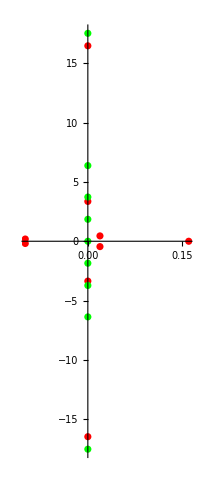

```mathematica
ComplexListPlot[{w[3],w[4]},PlotRange->All,PlotStyle->{Red,Green}]
```

```mathematica
w[1]=x/.NSolve[p[x]==0,x]
```

{0.171573,0.171573,5.82843,5.82843}

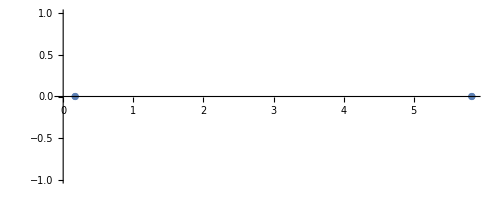

```mathematica
ComplexListPlot[w[1]]
```

```mathematica
w[2]=x/.NSolve[q[x]==0,x]
```

{3.-3.69552 ⅈ,3.+3.69552 ⅈ,3.-1.53073 ⅈ,3.+1.53073 ⅈ}

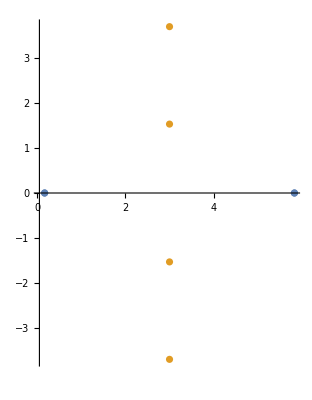

```mathematica
ComplexListPlot[{w[1],w[2]},PlotRange->All]
```

```mathematica
SO44c=SO4.SO4c
```

{{3.34315+5.65685 ⅈ,-10.2426-4.24264 ⅈ,5.65685+0. ⅈ,10.2426+4.24264 ⅈ},{-1.75736-4.24264 ⅈ,9.+5.65685 ⅈ,-10.2426-4.24264 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.75736-4.24264 ⅈ,9.+5.65685 ⅈ,-10.2426-4.24264 ⅈ},{1.75736+4.24264 ⅈ,-5.65685+0. ⅈ,-1.75736-4.24264 ⅈ,14.6569+5.65685 ⅈ}}

```mathematica
Det[SO44c]//Chop
```

257.

```mathematica
Tr[SO44c]
```

36.+22.6274 ⅈ

```mathematica
u[3]=N[Eigenvalues[SO44c]]
```

{17.4003+17.574 ⅈ,17.3302+5.88857 ⅈ,0.698255-0.572223 ⅈ,0.571288-0.262969 ⅈ}

```mathematica
s[x_]=CharacteristicPolynomial[SO44c,x]//Chop
```

257.-(612.+339.411 ⅈ) x+(262.+407.294 ⅈ) x^2-(36.+22.6274 ⅈ) x^3+x^4

```mathematica
o[z_,3]=Integrate[s[x]^2,{x,-z,z}]
```

(0.+0. ⅈ)+132098. z+(262675.+416525. ⅈ) z^3-(27210.4-106222. ⅈ) z^5+(373.714+698.217 ⅈ) z^7+0.222222 z^9

```mathematica
o[z_,4]=Integrate[p[x]*q[z],{x,-z,z}]
```

514. z-408. z^2+6650.67 z^3-5192. z^4+1878.13 z^5-385.6 z^6+53.3333 z^7-4.8 z^8+(2 z^9)/5

```mathematica
w[5]=z/.NSolve[o[z,4]==0,z]
```

{0.,0.-0.281151 ⅈ,0.+0.281151 ⅈ,0.-7.95326 ⅈ,0.+7.95326 ⅈ,3.-3.69552 ⅈ,3.+3.69552 ⅈ,3.-1.53073 ⅈ,3.+1.53073 ⅈ}

```mathematica
w[6]=z/.NSolve[o[z,3]-1==0,z]
```

{-30.451+50.016 ⅈ,-4.45291+11.1454 ⅈ,-0.828737-1.87623 ⅈ,-0.261599-0.466518 ⅈ,7.57014×10^-6-1.36791×10^-15 ⅈ,0.261591+0.466518 ⅈ,0.828738+1.87623 ⅈ,4.45291-11.1454 ⅈ,30.451-50.016 ⅈ}

```mathematica
(*root test as ones and zero*)
```

```mathematica
FullSimplify[Table[o[w[3][[j]],1],{j,Length[w[3]]}]]//Chop
```

{1.,1.,1.,1.,1.+1.90735×10^-6 ⅈ,1.-1.90735×10^-6 ⅈ,1.,1.,1.}

```mathematica
FullSimplify[Table[o[w[4][[j]],2],{j,Length[w[4]]}]]//Chop
```

{1.,1.,1.+3.72529×10^-9 ⅈ,1.-3.72529×10^-9 ⅈ,1.+6.85453×10^-6 ⅈ,1.-6.85453×10^-6 ⅈ,1.+4.65661×10^-10 ⅈ,1.-4.65661×10^-10 ⅈ,1.}

```mathematica
FullSimplify[Table[o[w[5][[j]],4],{j,Length[w[4]]}]]//Chop
```

{0,0,0,-1.86265×10^-8-2.23517×10^-8 ⅈ,-1.86265×10^-8+2.23517×10^-8 ⅈ,-1.16415×10^-10,-1.16415×10^-10,0,0}

```mathematica
FullSimplify[Table[o[w[6][[j]],3],{j,Length[w[6]]}]]//Chop
```

{1.49586-0.0816345 ⅈ,1.00001-1.19209×10^-6 ⅈ,1.-4.65661×10^-10 ⅈ,1.,1.,1.,1.+9.31323×10^-10 ⅈ,0.999996+7.7486×10^-6 ⅈ,1.00428-0.355728 ⅈ}

```mathematica
ph[x_,1]=x^2*q[x]/p[x]
```

(x^2 (257.-204. x+70. x^2-12. x^3+x^4))/(1-12 x+38 x^2-12 x^3+x^4)

```mathematica
ph[z_,2]=z^2*(o[z,2]-1)/(o[z,1]-1)
```

(z^2 (-1.+132098. z+51730.7 z^3+4124. z^5+81.1429 z^7+0.222222 z^9))/(-1+2 z+(440 z^3)/3+(3468 z^5)/5+(440 z^7)/7+(2 z^9)/9)

```mathematica
g1=JuliaSetPlot[ph[x,1]/N[2],x,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False];
```

```mathematica
g2=ListPlot[JuliaSetPoints[ph[x,1]/N[2],x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,AspectRatio->1];
```

```mathematica
Export["Julia_Cartan_SO4_Group_Sum_Hermanrings_scale2_both.jpg",{g1,g2}]
```

Julia_Cartan_SO4_Group_Sum_Hermanrings_scale2_both.jpg

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*scaled Cartan SO(4) Group Sum  Herman rings*)
```

```mathematica
f[x_]=(x^2 (257-204* x+70*x^2-12*x^3+x^4))/(1-12 x+38 x^2-12 x^3+x^4)
```

(x^2 (257-204 x+70 x^2-12 x^3+x^4))/(1-12 x+38 x^2-12 x^3+x^4)

```mathematica
(*Mandelbrot with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 28 Nov 2026 © *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 32) && (escapeCount < 1024) && (Abs[nz-nzold]>.5*10^(-3)),
		nzold=nz;
		nz=f[nz]/1.6795685937595257;
		++escapeCount
	];
	escapeCount*(1-Abs[Arg[nz]/(2*Pi)])
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-3.5,6.5,1000},{-5.,5.,1000}}];
```

```mathematica
g1=ListPlot3D[Log[1/Max[arraym]+arraym], Mesh -> False,AspectRatio -> 1,Boxed->False, Axes->False,ColorFunction->Hue,Background->Black,ViewPoint->Above,ImageSize->3000];
```

```mathematica
Export["j_1000_Cartan_SO4_Group3Sum_Hermanrings_scale1p6795685937595257_Arg_Monitor_g1.jpg",g1]
```

j_1000_Cartan_SO4_Group3Sum_Hermanrings_scale1p6795685937595257_Arg_Monitor_g1.jpg

```mathematica
arraym=FractalPureM[{{-3.5,6.5,1500},{-5.,5.,1500}}];
```

```mathematica
g2=ListDensityPlot[Abs[Log[1+arraym]],Mesh -> False,AspectRatio -> 1,ColorFunction->"DarkRainbow",ImageSize->3000,Frame->False];
```

```mathematica
Export["j_1500_Cartan_SO4_Group3Sum_Hermanrings_scale1p6795685937595257_Arg_Monitor_g2.jpg",g2]
```

j_1500_Cartan_SO4_Group3Sum_Hermanrings_scale1p6795685937595257_Arg_Monitor_g2.jpg

```mathematica
g3=ListDensityPlot[arraym,Mesh -> False, AspectRatio -> 1, ColorFunction->"DarkBands",ImageSize->3000,Frame->False];
```

```mathematica
Export["j_1500_Cartan_SO4_Group3Sum_Hermanrings_scale1p6795685937595257_Arg_Monitor_g3.jpg",g3]
```

j_1500_Cartan_SO4_Group3Sum_Hermanrings_scale1p6795685937595257_Arg_Monitor_g3.jpg

```mathematica
g4=ListDensityPlot[arraym, Mesh -> False, AspectRatio -> 1,ColorFunction->(Hue[#]&),ImageSize->3000,Axes->False,Frame->False];
```

```mathematica
Export["j_1500_Cartan_SO4_Group3Sum_Hermanrings_scale1p6795685937595257_Arg_Monitor_g4.jpg",g4]
```

j_1500_Cartan_SO4_Group3Sum_Hermanrings_scale1p6795685937595257_Arg_Monitor_g4.jpg

```mathematica
g5=ListDensityPlot[Log[1/Max[arraym]+arraym],Mesh -> False, AspectRatio ->1, ColorFunction->(Hue[#*1.15]&),ImageSize->3000,Axes->False,Frame->False];
```

```mathematica
Export["j_1500_Cartan_SO4_Group3Sum_Sum_Hermanrings_scale1p6795685937595257_Arg_Monitor_g5.jpg",g5]
```

j_1500_Cartan_SO4_Group3Sum_Sum_Hermanrings_scale1p6795685937595257_Arg_Monitor_g5.jpg

```mathematica
(*Fonction pour colorier des isocontours,exemple d'utilisation typique:ContourPlot[T[x,y],{x,-10,10},{y,-10,10},ColorFunction->cf]*)
(*http://perso.ensem.inpl-nancy.fr/Emmanuel.Plaut/mathematica/mycolorfunction.m*)
colortab=Reverse[Union[Join[{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}*1.25,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.25,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3]]];
```

```mathematica
ln=Length[colortab]
```

318

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/ln,1,Ceiling[ln* l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g6=ListDensityPlot[Log[1/Max[arraym]+arraym], Mesh -> False, AspectRatio -> 1, ColorFunction->cf,ImageSize->3000,Frame->False];
```

```mathematica
Export["j_1500_Cartan_SO4_Group3Sum_Hermanrings_scale1p6795685937595257_Arg_Monitor_g6.jpg",g6]
```

j_1500_Cartan_SO4_Group3Sum_Hermanrings_scale1p6795685937595257_Arg_Monitor_g6.jpg

```mathematica
Export["j_1500_Cartan_SO4_Group3Sum_Hermanrings_scale1p6795685937595257_Arg_Monitor_grid.jpg",GraphicsGrid[{{g1,g2}, 
 {g3,g4},{g5,g6}},ImageSize->{6000,9000}]]
```

j_1500_Cartan_SO4_Group3Sum_Hermanrings_scale1p6795685937595257_Arg_Monitor_grid.jpg

```mathematica
(*end*)
```